```mathematica
p2 >= p1 => x_r is the cheaper asset.;
t = p2/(p1+p2) is the intersection with the 45 degree line.;
M > 0;
r1 < r2 => the optimal allocation of agent 1 is closer to the x_r axis.;
```

1-1/ⅇ

1-1/(√ⅇ)

0.31606

0.196735

-Graphics-

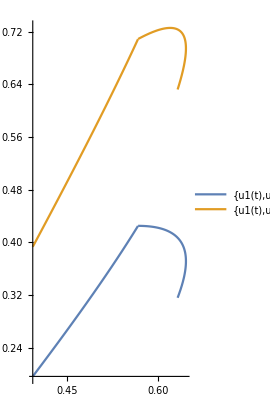

```mathematica
p1=1;
p2=2; 
M=1;
r1=1;
a1=1;
r2=1;
a2=0.5;
r3=1;
a3=1.5;
u1[t_]:=Min[a1*(1-Exp[(1-t)*(M/p1)*(-r1)])+1*(1-Exp[t*(M/p2)*(-r1)]),1*(1-Exp[(1-t)*(M/p1)*(-r1)])+a1*(1-Exp[t*(M/p2)*(-r1)])];
u2[t_]:=Min[a2*(1-Exp[(1-t)*(M/p1)*(-r2)])+1*(1-Exp[t*(M/p2)*(-r2)]),1*(1-Exp[(1-t)*(M/p1)*(-r2)])+a2*(1-Exp[t*(M/p2)*(-r2)])];
u3[t_]:=Min[a3*(1-Exp[(1-t)*(M/p1)*(-r3)])+1*(1-Exp[t*(M/p2)*(-r3)]),1*(1-Exp[(1-t)*(M/p1)*(-r3)])+a3*(1-Exp[t*(M/p2)*(-r3)])];
u1[0]
u1[1]
u2[0]
u2[1]
Plot[{u1[t],u2[t],u3[t]},{t,0,1},PlotLabels->"Expressions"]
ParametricPlot[{{u1[t],u2[t]},{u1[t],u3[t]}},{t,0,1},PlotLegends->"Expressions"]
```

0.31606

0.243291

0.252848

0.194633

-Graphics-

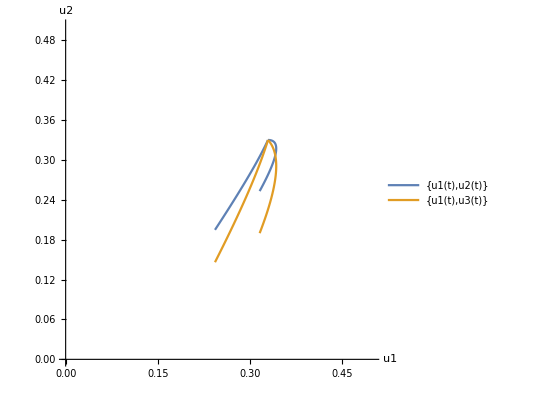

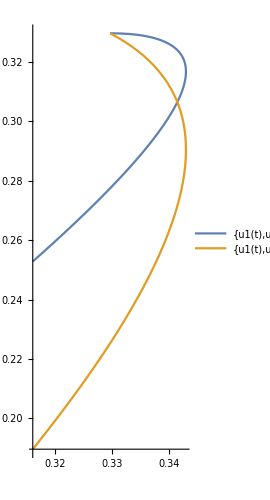

```mathematica
p1=1;
p2=1.5;
M=1;
r1=1;
a1=0.5;
r2=1;
a2=0.4; 
r3=1;
a3=0.3;
u1[t_]:=a1*(1-Exp[Max[(1-t)*(M/p1),t*(M/p2)]*(-r1)])+(1-a1)*(1-Exp[Min[(1-t)*(M/p1),t*(M/p2)]*(-r1)]);
u2[t_]:=a2*(1-Exp[Max[(1-t)*(M/p1),t*(M/p2)]*(-r2)])+(1-a2)*(1-Exp[Min[(1-t)*(M/p1),t*(M/p2)]*(-r2)]);
u3[t_]:=a3*(1-Exp[Max[(1-t)*(M/p1),t*(M/p2)]*(-r3)])+(1-a3)*(1-Exp[Min[(1-t)*(M/p1),t*(M/p2)]*(-r3)]);
u1[0]
u1[1]
u2[0]
u2[1]
Plot[{u1[t],u2[t],u3[t]},{t,0,1},PlotLabels->"Expressions"]
ParametricPlot[{{u1[t],u2[t]},{u1[t],u3[t]}},
{t,0,1},
PlotLegends->"Expressions",
PlotStyle->Thick,
AxesLabel->{u1,u2},
PlotRange->{0,0.5}
]
ParametricPlot[{{u1[t],u2[t]},{u1[t],u3[t]}},{t,0,p2/(p1+p2)},PlotLegends->"Expressions"]
```

0.31606

0.196735

0.388435

0.263817

-Graphics-

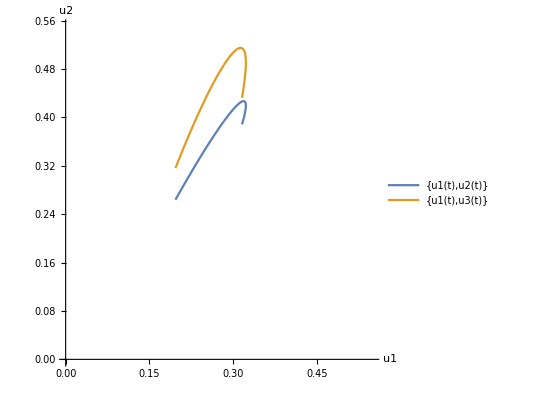

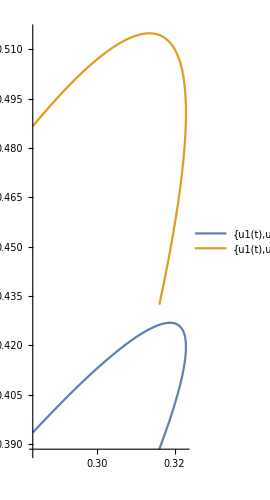

```mathematica
p1=1;
p2=2;
M=1;
r1=1;
a1=0.5;
r2=1.5;
a2=0.5;
r3=2;
a3=0.5;
u1[t_]:=a1*(1-Exp[Max[(1-t)*(M/p1),t*(M/p2)]*(-r1)])+(1-a1)*(1-Exp[Min[(1-t)*(M/p1),t*(M/p2)]*(-r1)]);
u2[t_]:=a2*(1-Exp[Max[(1-t)*(M/p1),t*(M/p2)]*(-r2)])+(1-a2)*(1-Exp[Min[(1-t)*(M/p1),t*(M/p2)]*(-r2)]);
u3[t_]:=a3*(1-Exp[Max[(1-t)*(M/p1),t*(M/p2)]*(-r3)])+(1-a3)*(1-Exp[Min[(1-t)*(M/p1),t*(M/p2)]*(-r3)]);
u1[0]
u1[1]
u2[0]
u2[1]
Plot[{u1[t],u2[t],u3[t]},{t,0,1},PlotLabels->"Expressions"]
ParametricPlot[{{u1[t],u2[t]},{u1[t],u3[t]}},
{t,0,1},
PlotLegends->"Expressions",
PlotStyle->Thick,
AxesLabel->{u1,u2},
PlotRange->{0,0.55}
]
ParametricPlot[{{u1[t],u2[t]},{u1[t],u3[t]}},{t,0,p2/(p1+p2)},PlotLegends->"Expressions"]
```

```mathematica
% effect of a difference
```

```mathematica
u1[t_]:=a1*(1-Exp[(1-t)*(M/p1)*(-r1)])+(1-a1)*(1-Exp[t*(M/p2)*(-r1)]);
u2[t_]:=a2*(1-Exp[(1-t)*(M/p1)*(-r2)])+(1-a2)*(1-Exp[t*(M/p2)*(-r2)]);FullSimplify[D[u1[t],t]-D[u2[t],t]]
```

(M (-(-1+a1) ⅇ^(-(M r1 t)/p2) p1 r1-a1 ⅇ^((M r1 (-1+t))/p1) p2 r1+(-1+a2) ⅇ^(-(M r2 t)/p2) p1 r2+a2 ⅇ^((M r2 (-1+t))/p1) p2 r2))/(p1 p2)

```mathematica
u1[t_]:=a1*(1-Exp[(1-t)*(1)*(-r1)])+(1-a1)*(1-Exp[t*(1/p2)*(-r1)]);
u2[t_]:=a2*(1-Exp[(1-t)*(1)*(-r2)])+(1-a2)*(1-Exp[t*(1/p2)*(-r2)]);
FullSimplify[D[u1[t],t]-D[u2[t],t]]
```

(-(-1+a1) ⅇ^(-(r1 t)/p2) r1-a1 ⅇ^(r1 (-1+t)) p2 r1+(-1+a2) ⅇ^(-(r2 t)/p2) r2+a2 ⅇ^(r2 (-1+t)) p2 r2)/p2

```mathematica
%effect of r difference
```

```mathematica
u1[t_]:=a*(1-Exp[(1-t)*(1)*(-r1)])+(1-a)*(1-Exp[t*(1/p2)*(-r1)]);
u2[t_]:=a*(1-Exp[(1-t)*(1)*(-r2)])+(1-a)*(1-Exp[t*(1/p2)*(-r2)]);
FullSimplify[D[u1[t]-u2[t],r2]]
FullSimplify[D[u1[t],t]-D[u2[t],t]]
```

a ⅇ^(r2 (-1+t)) (-1+t)+((-1+a) ⅇ^(-(r2 t)/p2) t)/p2

(-(-1+a) ⅇ^(-(r1 t)/p2) r1-a ⅇ^(r1 (-1+t)) p2 r1+(-1+a) ⅇ^(-(r2 t)/p2) r2+a ⅇ^(r2 (-1+t)) p2 r2)/p2